# C5P7

```mathematica
Clear["Global`*"];
e = 1.60215 * 10^-19;
h = 6.62607 *10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
```

```mathematica
alpha = Sqrt[(2*m*e)/ℏ^2] * 10^-9;
```

```mathematica
PI[kL_, kR_] = MatrixExp[1/2*Log[kL/kR] *(PauliMatrix[1] - IdentityMatrix[2])];
PP[kx_,l_] = MatrixExp[-I*kx*l*PauliMatrix[3]];
```

```mathematica
width = 4;
vwell = -0.6;
L = 1;
```

```mathematica
kvacuum = alpha * Sqrt[en];
kwell = alpha * Sqrt[en - vwell];
```

```mathematica
mbarrier= PI[kvacuum,kwell].PP[kwell, width].PI[kvacuum, kwell];
M = mbarrier.PP[kvacuum,L].mbarrier.PP[kvacuum,L].mbarrier.PP[kvacuum,L].mbarrier.PP[kvacuum,L].mbarrier ;
```

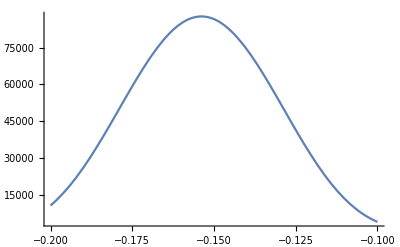

```mathematica
Plot[Abs[M[[1,1]]],{en,-.2,-0.1},PlotRange->All]
```

```mathematica
Clear["Global`*"];
e = 1.60215 * 10^-19;
h = 6.62607 *10^-34;
m = 9.10938 * 10^-31;
ℏ = h/(2*Pi);
```

```mathematica
alpha = Sqrt[(2*m*e)/ℏ^2] * 10^-9
PI[kL_, kR_] = MatrixExp[1/2*Log[kL/kR] *(PauliMatrix[1] - IdentityMatrix[2])];
PP[kx_,l_] = MatrixExp[-I*kx*l*PauliMatrix[3]];
```

5.12312

```mathematica
width = 4;
L = 1;
V = -0.6;
```

```mathematica
k = alpha * Sqrt[en];
kwell = alpha * Sqrt[en - V];
```

```mathematica
transfermatrix = PI[k,kwell].PP[kwell,width].PI[kwell,k].PP[k,L];
transfermatrix = MatrixPower[transfermatrix,4];
transfermatrix = transfermatrix.PI[k,kwell].PP[kwell,width].PI[kwell,k];
```

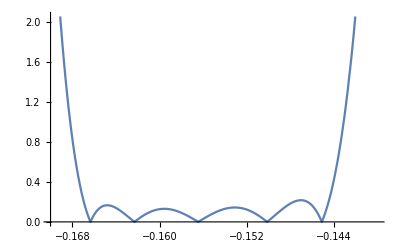

```mathematica
Plot[Abs[transfermatrix[[1,1]]],{en,-0.17,-0.14}]
```

```mathematica
FindRoot[Abs[transfermatrix[[1,1]]] == 0, {en,-0.17}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{en→-0.166337}

```mathematica
FindRoot[Abs[transfermatrix[[1,1]]] == 0, {en,-0.163}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{en→-0.162296}

```mathematica
FindRoot[Abs[transfermatrix[[1,1]]] == 0, {en,-0.156}]
```

{en→-0.15645}

```mathematica
FindRoot[Abs[transfermatrix[[1,1]]] == 0, {en,-0.150}]
```

{en→-0.150128}

```mathematica
FindRoot[Abs[transfermatrix[[1,1]]] == 0, {en,-0.146}]
```

{en→-0.145104}